```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Study number of junctions supported by ≥ K samples*)
```

```mathematica
aggregatedJunctionCounts=Drop[Import["hg19.sample.stats.tsv", "TSV"], 1];
```

```mathematica
totalJunctions = Transpose[Transpose[aggregatedJunctionCounts][[{1,2}]]];annotatedJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,3}]]];exonSkipJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,4}]]];altStartEndJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,5}]]];
novelJunctions=exonSkips=Transpose[Transpose[aggregatedJunctionCounts][[{1,6}]]];
```

```mathematica
exonSkipAnnotatedJunctions = Transpose[{annotatedJunctions[[All,1]],annotatedJunctions[[All,2]]+exonSkipJunctions[[All,2]]}];
someEvidenceJunctions = Transpose[{annotatedJunctions[[All,1]],annotatedJunctions[[All,2]]+exonSkipJunctions[[All,2]]+altStartEndJunctions[[All,2]]}];
```

```mathematica
mathematicaColors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Introduce levels of evidence, and annotated with junction counts for ≥ 1000 samples*)
```

```mathematica
labelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.033],Bold,TextAlignment->Left], y]
```

```mathematica
idx=16446-999
```

15447

```mathematica
bigLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.055],Bold,TextAlignment->Right], y]
```

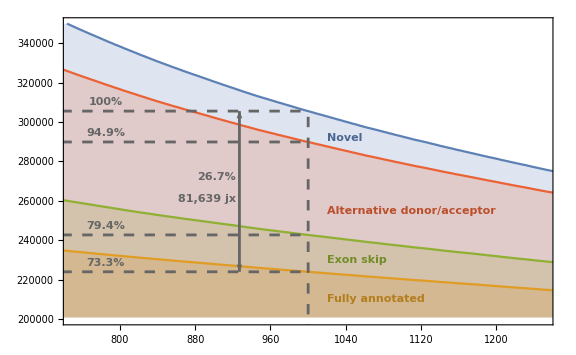

```mathematica
dashedColor=Darker[Gray,0.2];numberStartPos=785;insetAnnotationPlot=Show[ListPlot[{totalJunctions,annotatedJunctions,exonSkipAnnotatedJunctions, someEvidenceJunctions}, Joined->True, PlotRange->{{750, 1250},{200000,350000}}, Filling->Axis,  Frame->True,ImageSize->Large, BaseStyle->{FontFamily->"Arial",FontSize->15}], Graphics[{Directive[Thickness[0.0035],Dashing[0.013], dashedColor],Line[{{1000,0},totalJunctions[[idx]]}],Line[{{0,totalJunctions[[idx]][[2]]},totalJunctions[[idx]]}],Line[{{0,annotatedJunctions[[idx]][[2]]},annotatedJunctions[[idx]]}],
Line[{{0,exonSkipAnnotatedJunctions[[idx]][[2]]},exonSkipAnnotatedJunctions[[idx]]}],Line[{{0,someEvidenceJunctions[[idx]][[2]]},someEvidenceJunctions[[idx]]}],Directive[{Dashing[None],Arrowheads[{-.05,.05}]}], Arrow[{{927,annotatedJunctions[[idx]][[2]]},{927,totalJunctions[[idx]][[2]]}}],bigLabelForm[ToString[NumberForm[N[100-annotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%",{923, 272000}, {1,0}],labelForm[ToString[NumberForm[totalJunctions[[idx,2]]-annotatedJunctions[[idx,2]],DigitBlock->3]]<>" jx", {923, 261000},{1,0}],labelForm["100%",{numberStartPos,totalJunctions[[idx]][[2]]+4500}],labelForm[ToString[NumberForm[N[someEvidenceJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,someEvidenceJunctions[[idx]][[2]]+4500}],
labelForm[ToString[NumberForm[N[annotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,annotatedJunctions[[idx]][[2]]+4500}],
labelForm[ToString[NumberForm[N[exonSkipAnnotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100,3],DigitBlock->3]]<>"%", {numberStartPos,exonSkipAnnotatedJunctions[[idx]][[2]]+4500}],(*Directive[Thickness[0.0035],Arrowheads[.035],Dashing[None], dashedColor],Arrow[{{1000,totalJunctions[[idx]][[2]]+41000},{1000,totalJunctions[[idx]][[2]]+100}}],labelForm[ToString[NumberForm[N[100-annotatedJunctions[[idx,2]]/totalJunctions[[idx,2]]*100],3]]<>"% of jx unannotated, but\n"<>ToString[NumberForm[someEvidenceJunctions[[idx,2]]/totalJunctions[[idx,2]]*100//N,3]]<>"% of jx have donor and/or\nacceptor site in annotation", {1005, 330000}, {-1,0}],*)Darker[mathematicaColors[[1]], 0.2],labelForm["Novel",{1020,292000}, {-1,0}],Darker[mathematicaColors[[4]], 0.2],labelForm["Alternative donor/acceptor",{1020,255000}, {-1,0}],Darker[mathematicaColors[[3]], 0.2],labelForm["Exon skip",{1020,230000}, {-1,0}],Darker[mathematicaColors[[2]], 0.2],labelForm["Fully annotated",{1020,210000}, {-1,0}]}]]
```

```mathematica
baseImageSize={576,408}*1.3
```

{748.8,530.4}

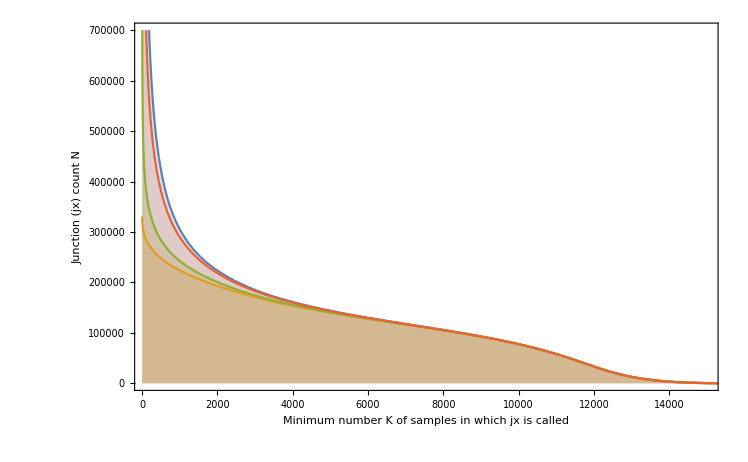

```mathematica
bigAnnotationPlot=ListPlot[{totalJunctions,annotatedJunctions,Transpose[{Transpose[annotatedJunctions][[1]],Transpose[annotatedJunctions][[2]]+Transpose[exonSkipJunctions][[2]]}], Transpose[{Transpose[annotatedJunctions][[1]],Transpose[annotatedJunctions][[2]]+Transpose[exonSkipJunctions][[2]]+Transpose[altStartEndJunctions][[2]]}]}, Joined->True, PlotRange->{{100, 15000},{0,700000}}, Filling->Axis,  Frame->True,ImageSize->baseImageSize, BaseStyle->{FontFamily->"Arial",FontSize->15},Epilog->Inset[insetAnnotationPlot, {9000,420000}, Automatic, 11000],FrameLabel->{Style["Minimum number K of samples in which jx is called", 22], Style["Junction (jx) count N", 22]}]
```

```mathematica
magnifyingGlass=Import["mag.png"]
```

-Graphics-

```mathematica
fig1a=Show[bigAnnotationPlot,Graphics[{EdgeForm[Directive[Gray, Thickness[.0015]]],Transparent,Rectangle[{750, 200000},{1250,350000}]}],Graphics[{Gray,Arrow[{{1400,300000},{3500,380000}}]}],  Graphics[{Opacity[0.5],Inset[magnifyingGlass,{1800,320000},{0,0},700]}], Graphics[{Black, Text[Style["a", FontFamily->"Arial", FontSize->40], {1000, 640000}]}],ImageSize->baseImageSize]
```

-Graphics-

```mathematica
statsBySample=Drop[Import["!awk '$6>=100000' "<>NotebookDirectory[]<>"hg19.stats_by_sample.tsv", "TSV"], 1];
```

```mathematica
jxConsidered=Length[statsBySample]
```

10311

```mathematica
(*overlaps by sample*)
```

```mathematica
largerLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.053],Bold,TextAlignment->Left], y]
```

```mathematica
jxHistList=HistogramList[statsBySample[[All,11]]/statsBySample[[All,10]]]
```

{{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1},{1,0,0,0,1,0,2,0,0,0,0,0,2,2,1,11,12,35,242,10002}}

```mathematica
lastBin=jxHistList[[2,20]]
```

10002

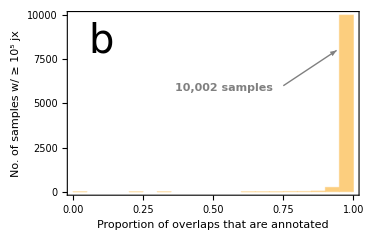

```mathematica
padding={{80,10},{60,0}};fig1b=Show[Histogram[statsBySample[[All,11]]/statsBySample[[All,10]]//N, Frame->True,ImageSize->baseImageSize*.5,BaseStyle->{FontFamily->"Arial",FontSize->15},ImagePadding->padding,FrameLabel->{Style["Proportion of overlaps that are annotated", 15], Style["No. of samples w/ ≥ 10^5 jx", 15]}],Graphics[{Gray,Arrow[{{0.75, 6000},{0.94,8000}}],largerLabelForm[ToString[NumberForm[lastBin,DigitBlock->3]]<>" samples", {0.54, 5900}]}],Graphics[{Black, Text[Style["b", FontFamily->"Avenir Next", FontSize->40], {0.1, 8500}]}]]
```

```mathematica
(*junctions by sample*)
```

```mathematica
jxHistList2=HistogramList[statsBySample[[All,7]]/statsBySample[[All,6]]]
```

{{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1},{1,0,1,1,1,1,18,27,90,132,148,307,474,803,1258,1522,2488,2214,822,3}}

```mathematica
lessThan80=Total[jxHistList2[[2,Range[1,16]]]]
```

4784

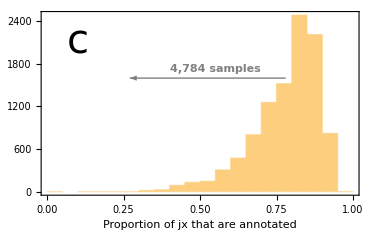

```mathematica
padding2={{70,10},{60,0}};fig1c=Show[Histogram[statsBySample[[All,7]]/statsBySample[[All,6]]//N, Frame->True,ImageSize->baseImageSize*.5,ImagePadding->padding2,BaseStyle->{FontFamily->"Arial",FontSize->15},FrameLabel->{Style["Proportion of jx that are annotated", 15], None}], Graphics[{Gray,Arrow[{{0.78, 1600},{0.27,1600}}], largerLabelForm[ToString[NumberForm[lessThan80,DigitBlock->3]]<>" samples", {0.55, 1730}]}],Graphics[{Black, Text[Style["c", FontFamily->"Arial", FontSize->40], {0.1, 2100}]}]]
```

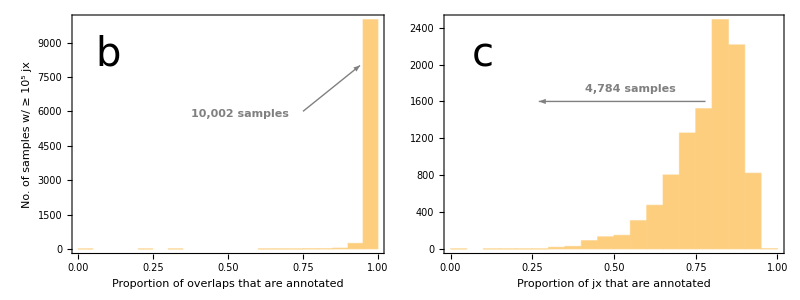
-Graphics-
-Graphics-

```mathematica
fig1=Grid[{{fig1a},{Grid[{{fig1b,fig1c}}]}}]
```

```mathematica
Export["jxannotation.pdf",fig1]
```

jxannotation.pdf

```mathematica
junctionsEvidenceVsDatesGeq20=Drop[Import["!gzip -cd hg19.sample_count_submission_date_overlap_geq_20.tsv.gz", "TSV"], 1];
```

```mathematica
junctionsEvidenceVsDatesGeq[x_]:= Select[junctionsEvidenceVsDatesGeq20,#[[1]]≥x &];talliedJunctionsGeq[x_]:=SortBy[Tally[junctionsEvidenceVsDatesGeq[x][[All,4]]], First];accumulatedJunctionsGeq[x_]:=(talliedJunctions=talliedJunctionsGeq[x];Transpose[{talliedJunctions[[All,1]],Accumulate[talliedJunctions[[All,2]]]}])
```

```mathematica
(*Convert from days after 2/27/2009 to dates*)
```

```mathematica
daysToDate = DateObject[{2009, 2, 27}]+LinguisticAssistant &
```

Fri 27 Feb 2009+#1&

```mathematica
(*When were junctions supported by reads in ≥ 20, 40, 80, 160 reads across samples found?*)
```

```mathematica
twentyThirteen=1404;daysToDate[twentyThirteen]
```

Tue 1 Jan 2013

```mathematica
dateFormat={"Month","/","Day","/","YearShort"};
```

```mathematica
(*Design ticks to intersect 1/1/2013*)
```

```mathematica
dateTicks=({#,DateString[daysToDate[#], dateFormat]}&/@Range[0, 2070, 234])
```

{{0,02/27/09},{234,10/19/09},{468,06/10/10},{702,01/30/11},{936,09/21/11},{1170,05/12/12},{1404,01/01/13},{1638,08/23/13},{1872,04/14/14}}

```mathematica
lastDay=Max[junctionsEvidenceVsDatesGeq20[[All,4]]]
```

2070

```mathematica
dateTicks=Append[dateTicks, {lastDay,DateString[daysToDate[lastDay], dateFormat]}]
```

{{0,02/27/09},{234,10/19/09},{468,06/10/10},{702,01/30/11},{936,09/21/11},{1170,05/12/12},{1404,01/01/13},{1638,08/23/13},{1872,04/14/14},{2070,10/29/14}}

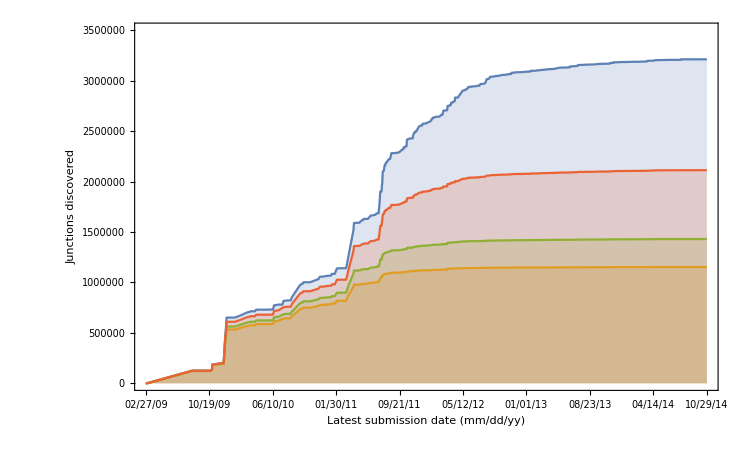

```mathematica
baseJunctionsPlot=ListPlot[accumulatedJunctionsGeq/@{20,120, 80,40}, Joined->True,Filling->Axis, Frame->True, FrameTicks->{{Automatic,None},{dateTicks, None}},BaseStyle->{FontFamily->"Avenir Next",FontSize->14}, FrameLabel->{Style["Latest submission date (mm/dd/yy)", 22], Style["Junctions discovered", 22]}, ImageSize->baseImageSize, PlotRange->{All, {0, 3.5*10^6}}]
```

```mathematica
sortedDays= Sort[junctionsEvidenceVsDates[[All,3]]];
```

```mathematica
commons=Commonest[sortedDays,5]
```

{293,298,748,766,865}

```mathematica
junctionsInCommons=Count[sortedDays, #]&/@Commonest[sortedDays,7]
```

{123759,124121,155069,163007,124664,252628,162196}

```mathematica
daysToDate/@Commonest[sortedDays,7]
```

{Sun 16 Aug 2009,Mon 14 Dec 2009,Thu 17 Dec 2009,Tue 22 Dec 2009,Thu 17 Mar 2011,Mon 4 Apr 2011,Tue 12 Jul 2011}

```mathematica
(*Some of these dates correspond to jumps in the plot above. Grepping for the submission dates in biosample_tags.tsv gives samples in the following projects:
3. Study of 69 LCLs (2)(Understanding mechanisms underlying human gene expression variation with RNA sequencing, by Pickrell et al.) 17 Dec 2009
4. Study of 41 Coriell cell lines (SRP001563)(Polymorphic cis-and trans-regulation of human gene expression, by Cheung et al.) 22 Dec 2009
5. Illumina bodyMap2 (ERP000546) 17-Mar-2011
6. University of Washington Human Reference Epigenome Mapping Project (SRP001371)(total RNA, fetal tissues, contributed most junctions on a single day (4 April 2011) at 252,628)
7. ENCODE long RNA-seq from CSHL (SRP007461) 12-Jul-2011

Annotate plot with the top 4 projects; the 1st, 2nd, and 5th are about the same size but have many fewer junctions than the top 4 contributors*)
```

```mathematica
arrowLabelForm [x_,y___]:= Text[Style[x, FontFamily->"Arial", FontSize->Scaled[.03],Bold,TextAlignment->Left], y]
```

```mathematica
accJunc=accumulatedJunctionsGeq[20];
```

```mathematica
maxAtTwentyThirteen=Select[accJunc, #[[1]]<=twentyThirteen &][[-1]][[2]]
```

3087471

```mathematica
maxAtEnd=accJunc[[-1]][[2]]
```

3211228

```mathematica
(*How many junctions covered by ≥ 20 reads are there?*)
```

```mathematica
Length[junctionsEvidenceVsDates]
```

3211228

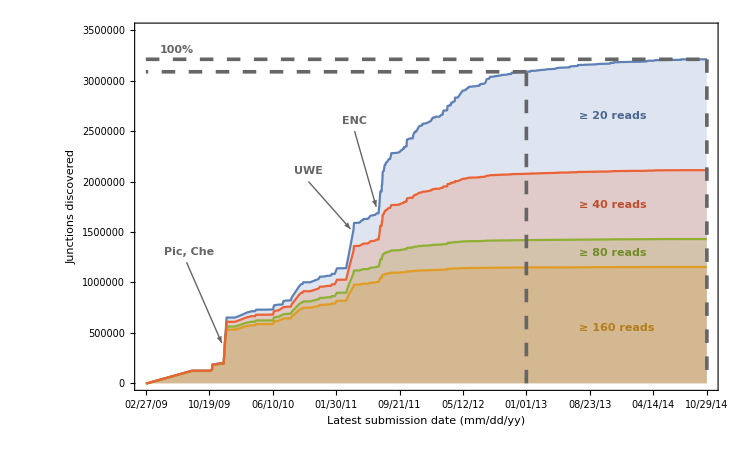

```mathematica
labelColor=Darker[Gray,0.2];leftPos=1600;fig2=Show[baseJunctionsPlot, Graphics[{labelColor,Arrow[{{150,1.2*10^6},{280,400000}}],arrowLabelForm["Pic, Che", {160,1.3*10^6}],Arrow[{{600,2*10^6},{755,1.53*10^6}}],arrowLabelForm["UWE", {600,2.1*10^6}],Arrow[{{770,2.5*10^6},{850,1.75*10^6}}],arrowLabelForm["ENC", {770,2.6*10^6}], Directive[Thickness[0.0035],Dashing[0.013], labelColor],Line[{{twentyThirteen,0},{twentyThirteen,maxAtTwentyThirteen}}],Line[{{twentyThirteen,maxAtTwentyThirteen},{0,maxAtTwentyThirteen}}],Line[{{lastDay,maxAtEnd},{lastDay,0}}],Line[{{0,maxAtEnd},{lastDay,maxAtEnd}}],arrowLabelForm["100%", {50, 3.3*10^6}, {-1,0}],Darker[mathematicaColors[[2]],0.2],arrowLabelForm["≥ 160 reads", {leftPos, 550000}, {-1,0}],Darker[mathematicaColors[[3]],0.2],arrowLabelForm["≥ 80 reads", {leftPos, 1.29*10^6}, {-1,0}],Darker[mathematicaColors[[4]],0.2],arrowLabelForm["≥ 40 reads", {leftPos, 1.77*10^6}, {-1,0}],Darker[mathematicaColors[[1]],0.2],arrowLabelForm["≥ 20 reads", {leftPos,  2.65*10^6}, {-1,0}]}]]
```

```mathematica
Export["dateplot.pdf", datePlot]
```

dateplot.pdf

```mathematica
GTAGJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,7}]]];
annotatedGTAGJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,8}]]];GCAGJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,9}]]];
annotatedGCAGJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,10}]]];
ATACJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,11}]]];
annotatedATACJunctions=Transpose[Transpose[aggregatedJunctionCounts][[{1,12}]]];
```

```mathematica
junctionTotals=Transpose[GTAGJunctions][[2]]+Transpose[GCAGJunctions][[2]]+Transpose[ATACJunctions][[2]];
```

```mathematica
GTAGproportions=Transpose[{Transpose[GTAGJunctions][[1]],Transpose[GTAGJunctions][[2]]/junctionTotals}]//N;GCAGproportions=Transpose[{Transpose[GCAGJunctions][[1]],Transpose[GCAGJunctions][[2]]/junctionTotals}]//N;ATACproportions=Transpose[{Transpose[ATACJunctions][[1]],Transpose[ATACJunctions][[2]]/junctionTotals}]//N;
```

```mathematica
ListPlot[{GTAGproportions,Transpose[{Transpose[GTAGproportions][[1]],Transpose[GTAGproportions][[2]]+Transpose[GCAGproportions][[2]]}], Transpose[GTAGproportions][[2]]+Transpose[GCAGproportions][[2]]+Transpose[ATACproportions][[2]]}, Joined->True, PlotRange->{{100, 10000},{.9,1}}, Filling->Axis,  Frame->True,FrameTicksStyle->White, Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}, ImageSize->Full, BaseStyle->{FontName->"Avenir Next", FontSize->40}]
```

-Graphics-

```mathematica
GTAGproportions[[16447-10000]]
```

{10000.,0.989829}

```mathematica
GCAGproportions[[16447-10000]]
```

{10000.,0.00811388}

```mathematica
ATACproportions[[16447-10000]]
```

{10000.,0.0020574}

```mathematica
GTAGproportions[[16447-1000]]
```

{1000.,0.966794}

```mathematica
GCAGproportions[[16447-1000]]
```

{1000.,0.0230417}

```mathematica
ATACproportions[[16447-1000]]
```

{1000.,0.0101644}

```mathematica
annotatedJunctionTotals=Transpose[annotatedGTAGJunctions][[2]]+Transpose[annotatedGCAGJunctions][[2]]+Transpose[annotatedATACJunctions][[2]];
```

```mathematica
annotatedGTAGproportions=Transpose[{Transpose[annotatedGTAGJunctions][[1]],Transpose[annotatedGTAGJunctions][[2]]/annotatedJunctionTotals}]//N;annotatedGCAGproportions=Transpose[{Transpose[annotatedGCAGJunctions][[1]],Transpose[annotatedGCAGJunctions][[2]]/annotatedJunctionTotals}]//N;annotatedATACproportions=Transpose[{Transpose[annotatedATACJunctions][[1]],Transpose[annotatedATACJunctions][[2]]/annotatedJunctionTotals}]//N;
```

```mathematica
ListPlot[{annotatedGTAGproportions,Transpose[{Transpose[annotatedGTAGproportions][[1]],Transpose[annotatedGTAGproportions][[2]]+Transpose[annotatedGCAGproportions][[2]]}], Transpose[annotatedGTAGproportions][[2]]+Transpose[annotatedGCAGproportions][[2]]+Transpose[annotatedATACproportions][[2]]}, Joined->True, PlotRange->{{100, 10000},{.97,1}}, Filling->Axis,  Frame->True,FrameTicksStyle->White, Prolog->{White,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}, ImageSize->Full, BaseStyle->{FontName->"Avenir Next", FontSize->40}]
```

-Graphics-

```mathematica
annotatedGTAGproportions[[16447-1000]]
```

{1000.,0.988992}

```mathematica
annotatedGCAGproportions[[16447-1000]]
```

{1000.,0.0100564}

```mathematica
annotatedATACproportions[[16447-1000]]
```

{1000.,0.00095116}

```mathematica
annotatedGTAGproportions[[16447-10000]]
```

{10000.,0.991097}

```mathematica
annotatedGCAGproportions[[16447-10000]]
```

{10000.,0.00769002}

```mathematica
annotatedATACproportions[[16447-10000]]
```

{10000.,0.00121286}